## Procedures

### Procedures to get and set printing resolution for evaluation notebook

```mathematica
getPrintingResolutionForNotebook[] := 
Module[ {allOptions, printingOptions, newPrintingOptions},

allOptions = FullOptions[ EvaluationNotebook[] ];
printingOptions = PrintingOptions /. Cases[ allOptions, a_ /; First[ a ] === PrintingOptions ];

Cases[printingOptions, Verbatim[ Rule ][ "RasterizationResolution", _ ] ][[1]]
]
```

```mathematica
setPrintingResolutionForNotebook[ resolutionValueInDPI_ ] := 
Module[ {allOptions, printingOptions, newPrintingOptions},

allOptions = FullOptions[ EvaluationNotebook[] ];
printingOptions = PrintingOptions /. Cases[ allOptions, a_ /; First[ a ] === PrintingOptions ];

newPrintingOptions =  ReplaceAll[ printingOptions, Verbatim[ Rule ][ "RasterizationResolution", _ ]  :>   Rule[ "RasterizationResolution", resolutionValueInDPI  ] ];

SetOptions[ EvaluationNotebook[], PrintingOptions -> newPrintingOptions ]
]
```

```mathematica
setPrintingResolutionForNotebook[ 72 * 4 ]
```

### Procedure to set headers

```mathematica
setTestHeaders[ whatSubjectCode_, whatSemester_, whatYear_, whatTest_, isSolutionQ_, durationString_ ] := 
Module[ {nb, changingString, subjectCodeString},
nb = EvaluationNotebook[];

changingString = StringJoin[  "American University of Malta\n",
 whatSemester ,
" ",
If[ StringQ[ whatYear ] === True, whatYear, ToString[ whatYear ] ],
Which[ (isSolutionQ && Not[ StringQ[ whatTest ] ]) === True, " - Solution to Test ", 
(Not[ isSolutionQ ] && Not[ StringQ[ whatTest ] ]) === True, " - Test ", 
True, " " ], 
Which[ StringQ[ whatTest ] === True, whatTest, True, ToString[ whatTest ] ],
"  ",
If[durationString === "", "", "("],
Which[ StringQ[ durationString ], durationString,
durationString === Automatic, "1 hr 0 min",
True, "1 hr 0 min" ],
If[durationString === "", "", ")"]
];
subjectCodeString = If[ StringQ[ whatSubjectCode ] === True, whatSubjectCode, ToString[ whatSubjectCode ] ];


SetOptions[ nb,PageHeaders->{{Cell[TextData[{StyleBox[ subjectCodeString <> "\nN Fares",FontFamily->"Times",FontSize->12]}],"Text"],Cell[TextData[{StyleBox[changingString,FontFamily->"Times",FontSize->12]}],"Text"],Cell[TextData[{StyleBox["Page ",FontFamily->"Times",FontSize->12],CounterBox["Page"]}],"Text"]},{Cell[TextData[{StyleBox[subjectCodeString <> "\nN Fares",FontFamily->"Times",FontSize->12]}],"Text"],Cell[TextData[{StyleBox[changingString,FontFamily->"Times",FontSize->12]}],"Text"],Cell[TextData[{StyleBox["Page ",FontFamily->"Times",FontSize->12],CounterBox["Page"]}],"Text"]}},
PrintingOptions->{"FacingPages"->True,"FirstPageFace"->Right,"FirstPageFooter"->True,"FirstPageHeader"->True}]
]
```

```mathematica
$Fall = "Fall";
$Spring = "Spring";
```

### Load package

```mathematica
<<NFPackages`structuralMechanicsBook` // Quiet;
```

## Preparation

### Problem 1

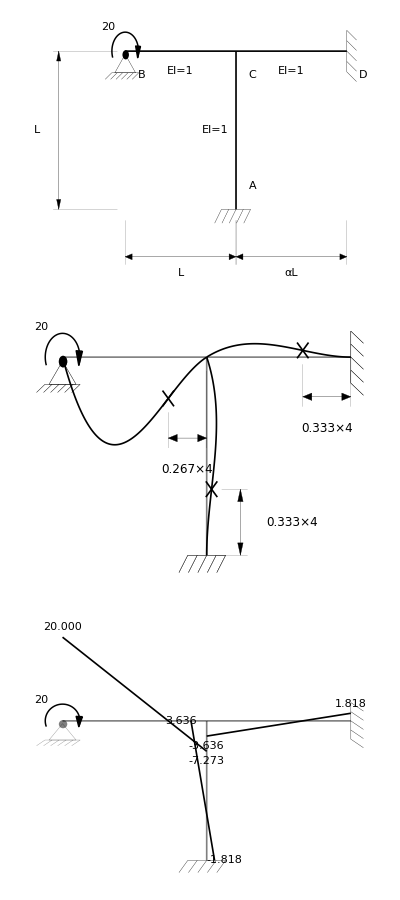

```mathematica
makeBuildingVerticalSpecsAndSolutionGrid[ {4}, {4, 4},300,
buildingBeamUniformLoadList -> { },
buildingBeamPointForceList -> { },
buildingNodeMomentApplied -> {{1, 1} -> -20},
buildingNodeMomentLabel-> "20",
buildingBeamsEIMagnitudeList -> {_ -> 1},
buildingBeamsEILabelList -> {},
buildingColumnsEIMagnitudeList -> {_ -> 1},
buildingColumnOmitList -> { {1, 1} -> True, {1, 2} -> False, {1, 3} -> True},
buildingBeamOmitList -> {},
buildingSideSupportLeftList -> {},
buildingSideSupportRightList -> { _ -> "fixed"},
buildingSupportList -> {1 -> "hinge", 2 -> "fixed"},
buildingFactorMomentDiagrams -> 0.02,
buildingDimensionLabelHeightList-> {_ -> "L"},
buildingDimensionLabelSpanList -> { 1->"L",2-> "αL"},
buildingSolveColumnBeamDisplacementFunctions -> False ]
```

#### Problem statement

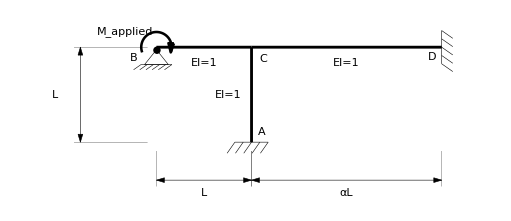

a) For α = 1, sketch the approximate deflected shape and show the location of all inflection points.
b) Given M_applied= 20 and α = 1, sketch the (exact) moment diagram.
c) For any value of M_applied and any value of α, determine M_CA/M_applied in terms of α and plot it.

#### Solution

a) For α = 1, sketch the approximate deflected shape.

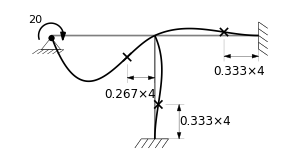

b) Given M_applied= 20 and α = 1, sketch the (exact) moment diagram.

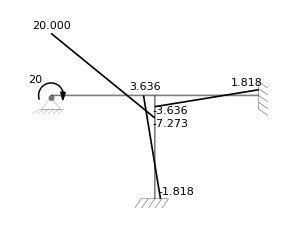

c) For any value of M_applied and any value of α, determine M_CA/M_applied in terms of α and plot it.

M_CB = (2k)/(3+4k) × M_B;          k = (4(EI/L)_AC + 4(EI/L)_CD)/(4(EI/L)_BC) = 1+1/α

Therefore (after simplifying):

M_BC = (2(1+α))/(4 +7α)M_applied

The distribution factor for member CA is:

DF_CA = (4(EI/L)_CA)/(4(EI/L)_CA + 4(EI/L)_CD) = 1/(1+1/α) = α/(1+α)

Therefore, M_CA is given by:

M_CA = DF_CA× M_BC = α/(1+α)×(2(1+α))/(4 +7α)M_applied = (2α)/(4 +7α)M_applied

⇒ M_CA/M_applied = (2α)/(4 +7α)

Plot:

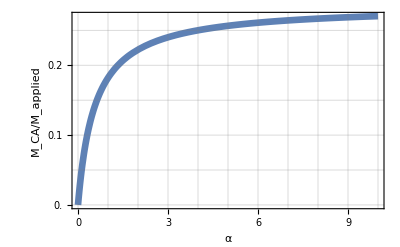

```mathematica
Plot[(2α)/(4+7α), {α, 0.0000000001, 10},
AxesOrigin->{0, 0},PlotRangePadding->None,
Frame-> True, FrameLabel -> {{"M_CA/M_applied", ""}, {"α", ""}},
RotateLabel -> False, PlotStyle -> Thickness[0.012],
GridLines -> {Range[0,10], Range[0,0.3,0.05]},
FrameTicks->{{Range[0,0.3,0.05], None}, {Range[0,10],None} }]
```

-Graphics-

### Problem 2

```mathematica
makeMemberIllustration[]
```

{{member,chord,label,internalHinge,inflectionPoint,momentCCW,momentCW,force|forceDown,forceUp,dimension,uniformLoad,hinge|hingeT,hingeA,fixed,spring,roller|rollerT,rollerA,fixedRollerA,fixedRollerT|fixedRoller,free|None,plot},{switchNormalQ,scaleFactor,referenceLength,heightFactor,lineThicknessFactor,lineColor,fillColor,springColor,rollerFillColor,forceOffsetVector,forceLocation,momentOffsetVector,momentLocation,momentShiftAngle,momentTotalAngle,displacementFunction,displacementScale,displacementAxial,showDisplacedQ,labelText,labelOffsetVector,labelLocation,internalHingeLocation,inflectionPointLocation,dimensionInterval,dimensionLineShift,dimensionText,dimensionTextShift,uniformLoadHeight,uniformLoadInterval,uniformLoadTextShift,uniformLoadText,plotFunction,plotFunctionInterval,plotFunctionScale,plotFunctionLocationList}}

```mathematica
makeMemberIllustration[{{0, 0}, {1, 0}}, {"referenceLength"-> 1}, {"lineThicknessFactor"->0.7,"member","uniformLoadHeight"->0.14, "uniformLoadInterval" -> {0, 1},"uniformLoadText" -> Style["w", 24],
 "uniformLoad",
"labelText" -> Style["P", 24],
"labelLocation" -> 0.5,"labelOffsetVector"-> {-0.05, 0.28}, "label",
"labelText" -> Style["EI", 20],
"labelLocation" -> 0.5,"labelOffsetVector"-> {0, -0.08}, "label",
"scaleFactor" -> 1.5, "forceLocation"-> 0.5,
"forceDown"
},
 {"labelText"-> Style["A", 18], "labelOffsetVector"-> (0.08{-1, 1}),
"label", "hinge"}, {"labelText"-> Style["B", 18], "labelOffsetVector"-> (0.08{1, 1}),
"label", "hinge"}] // Graphics // Show
```

```mathematica
WminOverPDimensional[30, 200, 1, 7.8]*2000
```

376.623

```mathematica
Solve[ 1==2  L^2/L0^2 1/W (1+W/2), W]
```

{{W→-(2 L^2)/(L^2-L0^2)}}

## Assignment

### Set title

```mathematica
setTestHeaders[ "CIE 418", $Fall, 2022, "Assignment 1", False, "" ]
```

### Problem 1

-Graphics-

a) For α = 1, sketch the approximate deflected shape.
b) Given M_applied= 20 and α = 1, sketch the (exact) moment diagram.
c) For any value of M_applied and any value of α, determine M_CA/M_applied in terms of α and plot it.

### Problem 2

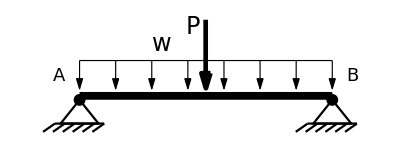

For a simple bridge with self-weight and a central force P applied, estimate the minimum total weight of the bridge in terms of:
	σ_Y yield stress of the beam material
	h    height of the beam (or truss)
	L    length of the beam
	γ   specific gravity of the beam material 
	P   applied central load

Estimate the minimum weight of the simple bridge for the following parameters:
σ_Y = 200 MPa, h = 1 m, L = 30 m, γ = 7.8, P = 2 × 10^3 × g N  (g ≈ 9.8 m/s^2;  so P is due to 2000 kg)

## Assignment Solution

### Set title

```mathematica
setTestHeaders[ "CIE 418", $Fall, 2022, "Solution to Assignment 1", False, "" ]
```

### Problem 1

-Graphics-

a) For α = 1, sketch the approximate deflected shape and show the location of all inflection points.
b) Given M_applied= 20 and α = 1, sketch the (exact) moment diagram.
c) For any value of M_applied and any value of α, determine M_CA/M_applied in terms of α and plot it.

#### Solution

a) For α = 1, sketch the approximate deflected shape.

-Graphics-

b) Given M_applied= 20 and α = 1, sketch the (exact) moment diagram.

-Graphics-

c) For any value of M_applied and any value of α, determine M_CA/M_applied in terms of α and plot it.

M_CB = (2k)/(3+4k) × M_B;          k = (4(EI/L)_AC + 4(EI/L)_CD)/(4(EI/L)_BC) = 1+1/α

Therefore (after simplifying):

M_BC = (2(1+α))/(4 +7α)M_applied

The distribution factor for member CA is:

DF_CA = (4(EI/L)_CA)/(4(EI/L)_CA + 4(EI/L)_CD) = 1/(1+1/α) = α/(1+α)

Therefore, M_CA is given by:

M_CA = DF_CA× M_BC = α/(1+α)×(2(1+α))/(4 +7α)M_applied = (2α)/(4 +7α)M_applied

⇒ M_CA/M_applied = (2α)/(4 +7α)

Plot:

-Graphics-

### Problem 2

For a simple bridge with self-weight and a central force P applied, estimate the minimum total weight of the bridge in terms of:
	σ_Y yield stress of the beam material
	h    height of the beam (or truss)
	L    length of the beam
	γ   specific gravity of the beam material 
	P   applied central load

Estimate the minimum weight of the simple bridge for the following parameters:
σ_Y = 200 MPa, h = 1 m, L = 30 m, γ = 7.8, P = 2 × 10^3 × g N  (g ≈ 9.8 m/s^2;  so P is due to 2000 kg)

#### Solution

We consider the optimal section which has a moment of inertia:

I = (A h^2)/4

The failure is assumed to occur when yielding starts (true for an I-beam which has the optimal moment of inertia):

σ_Y =(M_max h)/(2 I) = (M_max h)/(2 A h^2/4) = 2 M_max/(A h)

M_max for the combined loads are:

M_max = PL/4 +wL^2/8

The weight of the beam is given by:

W = w L

Therefore, M_max is given by:

M_max = PL/4 ( 1 +(Ŵ)/2)    where Ŵ = W/P  (What we’re trying to calculate)

Putting the failure with M_max together, we get:

σ_Y = 1/2 (P L)/(A h) ( 1 +(Ŵ)/2)

If we multiply and divide by γ ρ_water g L where ρ_beam = γ ρ_water, and noting that W = ρ_beam A L g, we get:

σ_Y = 1/2 (γ ρ_water g L P L)/(γ ρ_water g L A h) ( 1 +(Ŵ)/2) = 1/2 (γ ρ_water g P L^2)/(W h) ( 1 +(Ŵ)/2)

Define:

L_0= 2 √((σ_Y h)/(γ ρ_water g))

Note:  We can show that L_0 is the maximum length that a beam can be built without failing under its own weight

Then:

Ŵ = 2/((L_0/L)^2 - 1)

Given: 
σ_Y = 200 MPa, h = 1 m, L = 30 m, γ = 7.8, P = 2 × 10^3 × g N  (g ≈ 9.8 m/s^2;  so P is due to 2000 kg)

We get:

W_minimum = 377 kg